6.)

```mathematica
sizesAndTimes = 
Table[
{
n,
Timing[Det[RandomInteger[{1,10},{n,n}]]][[1]]
},
{n,50,500,50}
]
```

{{50,0.029889},{100,0.039177},{150,0.088771},{200,0.198428},{250,0.353505},{300,0.633161},{350,1.00762},{400,1.54272},{450,2.0839},{500,2.81833}}

a.)

```mathematica
cubic = Fit[sizesAndTimes,{1,x,x^2,x^3},x]
```

0.0922904-0.00142182 x+6.64983×10^-6 x^2+1.42337×10^-8 x^3

b.)

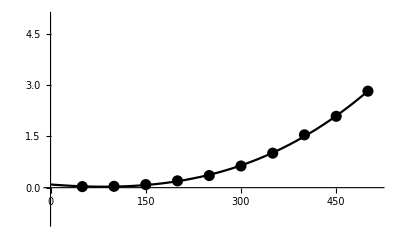

```mathematica
Plot[
cubic,
{x,0,500},
PlotStyle->Black,
PlotRange->{{0,515},{-1,5}},
Epilog->{
Black,PointSize[0.02],Point[sizesAndTimes]
}
]
```

c.)

```mathematica
x = 5000;
cubic
```

1938.45

The cubic function predicts 1938.45 seconds, which = 32.3 minutes

```mathematica
Timing[Det[RandomInteger[{1,10},{5000,5000}]]][[1]]
```

13866.4

It says it took over 3 hours and I did it overnight. I think this it has something to do with my computer sleep settings so I’m not sure if this is entirely accurate. I can’t run it again because it was really messing up my computer.

d.)

```mathematica
Clear[x];
Solve[cubic== 31 10^6,x]
```

{{x→-58578.6-101368. ⅈ},{x→-58578.6+101368. ⅈ},{x→116996.}}

You would need a 116996 x 116996 matrix for it to take one year to compute

e.)

When you are trying to find the LU factorization for an n  x  n matrix, it takes an order of n^3 operations to find. More specifically, the dominant term in the equation is 2n^3/3. The process of performing these operations can be done through several algorithms, including Gaussian elimination, which is essentially a more complicated version of how we’ve been row reducing, using variables such as u and l with various subscripts indicating their positions in the matrix. The reason this algorithm has a complexity of O(n^3) is because it requires n(n + 1)/2 divisions, (2n^3 + 3n^2 − 5n)/6 multiplications, and (2n^3 + 3n^2 − 5n)/6 subtractions, for a total of approximately 2n^3/3 operations. The proof of why Gaussian elimination takes these specific amounts of operations is in Farebrother, R.W. (1988), Linear Least Squares Computations, which is not free on the internet. Using  Gaussian elimination to find the lower and upper matrices is useful because it brakes up  a given matrix A into two different matrices L and U that are now easier to manipulate. Plus, it only has a complexity of O(n^3).

https://en.wikipedia.org/wiki/Gaussian_elimination#Computational_efficiency
https://math.stackexchange.com/questions/2554714/why-is-efficency-of-gaussian-elimination-on3